```mathematica
img=Import["https://web.mit.edu/puzzle/www/2019/assets/puzzles/picture_book/image.png"];
```

```mathematica
img
```

-Graphics-

```mathematica
bytes=ImageData[img,"Byte"];
```

The distribution is a bit odd:

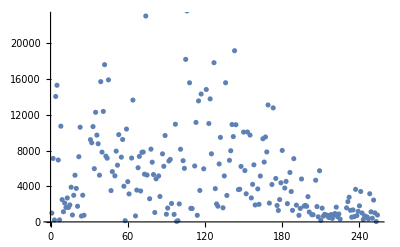

```mathematica
ListPlot[Tally[Flatten[bytes]]]
```

```mathematica
bytes[[1]][[1;;100]]
```

{97,127,153,117,117,115,117,0,175,153,0,239,108,89,128,117,0,239,85,153,87,128,0,172,0,173,123,136,123,115,127,153,0,206,100,97,89,112,0,175,97,150,78,0,189,97,127,116,113,141,108,105,0,150,136,89,131,0,186,121,120,89,0,167,124,101,0,173,123,108,113,121,124,115,108,106,0,175,115,108,121,113,105,141,0,165,0,175,120,155,91,0,169,119,0,127,136,123,124,115}

This is totally text. 0 is too overwhelmingly common to be an E, and it never occurs in doubles except at the very end, so it is padding of some sort.

```mathematica
First/@Position[Partition[Flatten[bytes],2,1],{0,0}]==Range[1450872,Length[Flatten[bytes]]-1]
```

True

```mathematica
SortBy[Tally[Flatten[bytes]],Last]//Reverse
```

{{0,269445},{65,43957},{120,24845},{106,23648},{74,23075},{143,19187},{105,18218},{127,17843},{42,17624},{45,15918},{39,15718},{136,15596},{108,15592},{5,15313},{121,14839},{117,14332},{4,14058},{124,13787},{64,13651},{115,13565},{169,13104},{173,12781},{41,12383},{35,12282},{113,11150},{123,11025},{97,10946},{141,10914},{144,10890},{8,10728},{33,10682},{23,10612},{59,10406},{153,10076},{150,10065},{53,9779},{155,9731},{36,9726},{89,9682},{142,9559},{167,9518},{132,9472},{165,9320},{56,9234},{31,9215},{32,8869},{37,8757},{78,8154},{101,8142},{180,8009},{140,7973},{51,7932},{168,7841},{72,7825},{40,7820},{71,7805},{125,7629},{87,7626},{43,7369},{69,7339},{22,7306},{55,7259},{63,7156},{44,7142},{2,7114},{189,7089},{93,7005},{6,6935},{139,6900},{103,6860},{92,6827},{166,6708},{79,6692},{131,6496},{158,6396},{52,6355},{112,6265},{88,6228},{148,6219},{68,6072},{104,6002},{34,5965},{119,5950},{151,5752},{209,5733},{48,5638},{186,5538},{73,5348},{80,5307},{75,5252},{38,5236},{19,5229},{50,5161},{135,5151},{84,5150},{163,5143},{175,4868},{82,4829},{195,4810},{206,4672},{183,4536},{60,4510},{179,4380},{157,4208},{172,4191},{57,3996},{16,3887},{182,3796},{20,3754},{128,3728},{161,3697},{147,3663},{237,3647},{146,3620},{67,3565},{116,3524},{47,3507},{70,3465},{241,3407},{187,3404},{248,3155},{152,3150},{61,3134},{25,2991},{18,2983},{137,2964},{85,2850},{200,2829},{232,2764},{156,2686},{13,2683},{77,2593},{178,2498},{9,2494},{251,2447},{231,2269},{11,2111},{170,2105},{94,2065},{184,2047},{100,2017},{129,2011},{162,1968},{15,1900},{159,1896},{191,1879},{198,1849},{176,1839},{240,1799},{197,1768},{130,1761},{21,1754},{199,1746},{207,1718},{222,1653},{14,1627},{12,1617},{134,1583},{230,1572},{91,1551},{211,1540},{109,1519},{194,1510},{110,1499},{235,1342},{233,1300},{188,1295},{177,1282},{239,1180},{10,1138},{249,1124},{201,1109},{81,1055},{252,1008},{242,997},{1,987},{221,944},{224,884},{90,860},{213,847},{96,838},{218,822},{203,808},{204,803},{220,792},{17,777},{254,768},{215,745},{26,745},{114,740},{193,734},{238,705},{244,671},{66,669},{24,656},{212,648},{236,589},{223,584},{208,570},{246,554},{245,547},{234,527},{216,522},{217,481},{250,411},{219,394},{247,337},{225,312},{243,267},{7,230},{3,217},{210,175},{58,138},{99,132},{98,58},{253,40}}

It just takes a little inspiration to see “ULYSSES” at the beginning; then it’s obvious that 0 is a space.

```mathematica
knownMapping=Transpose[{{97,127,153,117,117,115,117},Characters@"ulysses"}]
```

{{97,u},{127,l},{153,y},{117,s},{117,s},{115,e},{117,s}}

```mathematica
rules:=First@First@#->Map[Last,#]&/@GatherBy[knownMapping,First]
```

```mathematica
errors:=Select[rules,DeleteDuplicates@#[[2]]{#[[2]][[1]]}&]
```

```mathematica
contracted:=Dispatch@MapAt[First,rules,{All,2}]
```

```mathematica
Flatten[bytes]/.contracted/.{0->" ",_?NumericQ->"_"}//StringJoin
```

ulysses _y ____s __y__ _ ____ely __u__ _u__ _ul_____ ____ ____ ___ ______e__ _e_____ _ ____ __ l___e_ __ _____ _ ______ ___ _ _____ l__ ___sse_ _ y_____ __ess…                                                                                                                                                              
 |  |  |  |

Now just continue iteratively, it’s obviously “Ulysses by James Joyce”, etc.

```mathematica
knownMapping=With[{known="ulysses by james joyce"},Transpose[{Flatten[bytes][[;;StringLength[known]]],Characters@known}]]
```

{{97,u},{127,l},{153,y},{117,s},{117,s},{115,e},{117,s},{0, },{175,b},{153,y},{0, },{239,j},{108,a},{89,m},{128,e},{117,s},{0, },{239,j},{85,o},{153,y},{87,c},{128,e}}

And it’s clearly just the text of Ulysses.

```mathematica
knownMapping=Transpose[{{97,127,153,117,117,115,117,0,175,153,0,239,108,89,128,117,0,239,85,153,87,128,173,123,136,123,115,127,153,206,100,97,89,112,0,175,97,150,78,0,189,97,127,116,113,141,108,105,0,150,136,89,131,0,186,121,120,89,0,167,124,101,0,173,123,108,113,121,124,115,108,106},Characters@"ulysses by james joycestatelyplump buck mulligan came from the stairhead"}]
```

{{97,u},{127,l},{153,y},{117,s},{117,s},{115,e},{117,s},{0, },{175,b},{153,y},{0, },{239,j},{108,a},{89,m},{128,e},{117,s},{0, },{239,j},{85,o},{153,y},{87,c},{128,e},{173,s},{123,t},{136,a},{123,t},{115,e},{127,l},{153,y},{206,p},{100,l},{97,u},{89,m},{112,p},{0, },{175,b},{97,u},{150,c},{78,k},{0, },{189,m},{97,u},{127,l},{116,l},{113,i},{141,g},{108,a},{105,n},{0, },{150,c},{136,a},{89,m},{131,e},{0, },{186,f},{121,r},{120,o},{89,m},{0, },{167,t},{124,h},{101,e},{0, },{173,s},{123,t},{108,a},{113,i},{121,r},{124,h},{115,e},{108,a},{106,d}}

```mathematica
gutenberg=Import["https://www.gutenberg.org/files/4300/4300-0.txt"];
```

Text ends with “I will yes”:

```mathematica
Flatten[bytes][[1450872-20;;1450872]]
```

{0,63,57,59,106,0,75,65,63,0,79,0,155,42,39,81,0,75,65,45,0}

Get the text into a form where we can just automatically match it up with the bytes:

```mathematica
text=StringReplace[StringReplace[StringTake[ToUpperCase@gutenberg,First@First@StringPosition[gutenberg,"Stately"];;Last@Last@StringPosition[gutenberg,"I will Yes"]],{"\n"->" ","M.P."->"M P ","’"->" ","É"->"E","À" -> "A","È" -> "E","-"->" ","Î"->"I","C/O"->"C O","..."->" ",ToUpperCase@"œ"->"OE","Ü"->"U",RegularExpression["[^ A-Z]"]->""}],RegularExpression[" +"]->" "];
```

```mathematica
knownMapping=With[{n=140000},Transpose[{Flatten[bytes][[1;;n]],Characters[StringJoin["ULYSSES BY JAMES JOYCE I ",text]][[1;;n]]}]];
```

```mathematica
{Flatten[bytes][[130200;;130220]],Characters[StringJoin["ULYSSES BY JAMES JOYCE I ",text]][[130200;;130220]]}
```

{{0,213,0,191,0,175,165,106,141,163,0,198,165,153,139,140,0,194,0,194,127},{ ,T, ,A, ,B,A,D,G,E, ,M,A,Y,B,E, ,E, ,E,L}}

```mathematica
errors
```

{}

```mathematica
Range[255]/.(Rule@@@knownMapping)/._?NumericQ->"_"//Dynamic
```

That’s enough for “congratulations on your amazing steganography skills to complete puzzle find all pixels for the letter that begins the city where the author is buried, and form a new image in portrait orientation”. The city is Zurich, so Z.

```mathematica
zs=Join[Select[Rule@@@knownMapping//DeleteDuplicates,#[[2]]=="Z"&],{255->"Z"}]
```

{26→Z,58→Z,98→Z,99→Z,255→Z}

```mathematica
zBytes=Cases[Flatten@bytes,_?(MemberQ[First/@zs,#]&)];
```

```mathematica
Length@zBytes//FactorInteger
```

{{29,1},{37,1}}

```mathematica
ArrayPlot@Partition[zBytes,29]
```

-Graphics-